FittedModel[0.11773-0.00328734 x+0.0000180619 x^2]

FittedModel[1.03153-0.0208421 x+0.0000670767 x^2]

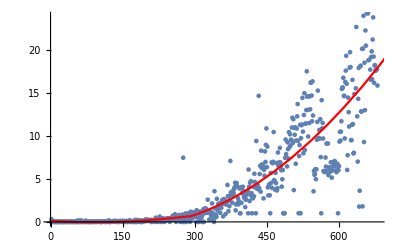

0.244945

0.841181

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "comma"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
linear = NonlinearModelFit[data[[1;;288]],a+b*x+c*x^2,{a,b,c},x]
quadratic = NonlinearModelFit[data[[289;;680]],a+b*x+c*x^2,{a,b,c},x]
Show[ListPlot[data],Plot[linear[x],{x,0,288},PlotStyle->Red],Plot[quadratic[x],{x,288,2048},PlotStyle->Red]]
linear["RSquared"]
quadratic["RSquared"]
```